## Annihilations

```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
tempConversion = (1*^-9/(1.16*^4)); (* GeV *)
NM     = mn =(0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
TT = (1*^5*3.154*^7)/(6.58*^-25); (* therm time *)
hBar = 1.054571800*^-34;
vd  = 200/cspeed;(* kms^-1/c *)
vn =  230 /cspeed;(* kms^-1 /c*)
cspeed=299792458;(*m/s*)
km=1000;(*km/m*)
cm=1/100;(*cm/m*)
Gevto1fm=1000/197.3;(*1/(GeV*fm)*)
fm1to1m=10^15;(*m/fm*)
ρχ = 0.4*(hbarc)^3*1*^6;  (*Gev^4*) 
hbarc = (0.1973269788*1.*^-15); (* GeV m *)
Prefactor=(1/cm)^3*(Gevto1fm^(-2))*fm1to1m*cspeed//Simplify;
ϵreg=10^(-4);
σSB = 5.67*^-8*6.582*^-25*(hbarc)^2/(1.60*^-10);


vAvg[mx_, temp_] := (6*temp*tempConversion)/mx;

capRate = 1.*^22*6.58*^-16*1*^-9; (*test cap rate*)
```

## NS Data

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = Rstar= 11.6;

μfn[x_]:= Interpolation[ EoSData[[All, {1,8}]] ][x*Rstar]*1*^-3; (* Chemical potential in GeV *)
μfe[x_]:= Interpolation[ EoSData[[All, {1,10}]] ][x*Rstar]*1*^-3;
μfμ[x_]:= Interpolation[ EoSData[[All, {1,11}]] ][x*Rstar]*1*^-3;

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = nb*Yn;
nprof=Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-3*)

MNS = Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *) 

p =Interpolation[EoSData[[All, {1, 12}]]]; (* in dyn/cm^2*)
```

```mathematica
NIntegrate[μfe[x], {x, 0, 1}]
```

0.169812

```mathematica
EscVelSetUp[rad_?NumericQ] := Module[                                                           (* escape velocity inside star, in natural units *)
{GravPot,r}, 
GravPot =NIntegrate[(2.*G*MNS[r]*2.*^30)/(r^2*1.*^3), {r, rad, rMax}];
Sqrt[GravPot +(2.*G*MNS[rMax]*2.*^30)/(rMax*1.*^3)]/cspeed
]; 


ve = Interpolation[Table[{ri, EscVelSetUp[ri]}, {ri, rMin, Last[radius]}]];
```

```mathematica
(*Define Rstar, ζ0, B[r], nprof[r] (the true baryon density, NOT energy density) and μf[r].
Rstar in kmeters
nprof in the unit you want, I use fm^-3
ζ0 in the right unit to match nprof and nfree (That is in GeV^3)
μf in GeV
 IMPORTANT: definitions have to be functions that can be evaluated fast!*)
```

```mathematica
rtA[r_]:=Sqrt[1/(1 -(2*G*MNS[r*Rstar]*2*^30)/(r*Rstar*1*^3*cspeed^2))];
```

```mathematica
Clear[B];
B =NDSolveValue[{y'[x]==(2*G*(Rstar*1*^3))/(cspeed^2*(x*(Rstar*1*^3))^2)*((MNS[x*Rstar]*2*^30+p[x*Rstar]*0.1*(x*(Rstar*1*^3))^3/cspeed^2)/( 1 - (2*G*MNS[x*Rstar]*2*^30)/(cspeed^2*(x*(Rstar*1*^3)))))*y[x], y[1]==(1 - (2*G*MNS[1*Rstar]*2*^30)/(cspeed^2*(Rstar*1*^3)))},y, {x, rMin/Rstar, 1}];
(*takes as input r/Rstar (from 0 to 1)*)
```

```mathematica
ζ0=5.278368626202642(*Note that is not a problem that it is >1, as I use different units for ntrue and nfree, in same units result is 0.04*);
```

```mathematica
rTh[T_, mx_]:=3.265*√(T/10^5)*√(1/mx);
```

```mathematica
ϕ[r_]:= (2*π*G*(7.76*1*^17)*r^2)/3;
```

```mathematica
ndAnFac[mx_?NumericQ, T_]:=(NIntegrate[x^2*Exp[(-2*x^2)/rTh[T,mx]^2],{x, 0, rTh[T, mx]}]*hbarc^3)/(4*π*(NIntegrate[x^2*Exp[-x^2/rTh[T,mx]^2],{x, 0, rTh[T, mx]}])^2);
```

## Masses and Form Factors

```mathematica
lepMasses = {0.5109989461, 105.6583745, 1776.86, 0,0,0}*1.*^-3;(* {e, μ, τ,Subscript[ν, e], Subscript[ν, μ], Subscript[ν, τ]}*)
quarkMasses = {2.2*^-3, 4.7*^-3, 95*^-3, 1.257, 4.18, 173};(* {u, d, s, c, b, t}  *)
```

```mathematica
fT = {Mean[{0.019, 0.022, 0.012, 0.011, 0.014, 0.018}], Mean[{0.041, 0.049, 0.033, 0.027, 0.036, 0.042}], Mean[{0.14, 0.36, 0.053, 0.045, 0.118, 0.26}]};

fTG = 1. - Sum[fT[[n]], {n, 1, 3}];

DeltaN = {Mean[{-0.4, -0.43, -0.44, -0.43, -0.48, -0.43}],Mean[{0.77, 0.86, 0.84, 0.84, 0.78, 0.84}], Mean[{-0.12, -0.09, -0.03, -0.085, -0.15, -0.08}]};

deltaN = { 0.23,-0.84, 0.05};(* {u, d, s} *)
```

```mathematica
c12 = Sum[(NM*fT[[n]])/quarkMasses[[n]],{n, 1,3}] +(2.*fTG)/27.*(Sum[NM/quarkMasses[[n]], {n, 3, 6}] - NM);
mBar = 1./Sum[1./quarkMasses[[n]], {n, 1, 3}];
C34 = Sum[mBar/quarkMasses[[n]],{n,1,6}];
c34 = Sum[NM/quarkMasses[[n]]*(1 - C34 +mBar)*DeltaN[[n]],{n, 1,3}];
c56 = 3.;
c78 = Sum[DeltaN[[n]], {n, 1, 3}];
c910 = Sum[deltaN[[n]], {n, 1, 3}];
```

```mathematica
μfeAvg = NIntegrate[μfe[x], {x, 0, 2/Rstar}]/(2/Rstar)
μfμAvg = NIntegrate[μfμ[x], {x, 0, 2/Rstar}]/(2/Rstar)
```

0.19701

0.0913518

```mathematica
lepMasses[[1]]
```

0.000510999

```mathematica
fde[mx_]:=HeavisideTheta[-μfeAvg+mx];
fdμ[mx_]:=HeavisideTheta[-μfμAvg +mx];
fdoth[mx_] := 1.;
fdSelect[mf_]:=Which[mf ==lepMasses[[1]], fde, mf == lepMasses[[2]], fdμ, True, fdoth];
test[mx_]:=Sum[fdSelect[mf][mx], {mf, Select[lepMasses, #≤ mx&]}]
```

## Cross sections Ann

```mathematica
d1ACS[mx_, temp_] :=(Sum[(mx^2/(16.*π*c12^2))*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp]*fdSelect[mf][mx], {mf, Select[lepMasses, #≤ mx&]}]+Sum[((3.*mx^2)/(16.*π*c12^2))*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp], {mf, Select[quarkMasses, #≤ mx&]}] );
(*================================================================================================================================================================*)
d2ACS[mx_, temp_] :=(Sum[(1./(16.*π*c12^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(8*(1 - mf^2/mx^2)+3vAvg[mx, temp])*fdSelect[mf][mx],{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(16.*π*c12^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(8*(1 - mf^2/mx^2)+3vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d3ACS[mx_, temp_] :=(Sum[(1./(8.*π*c34^2))*mx^2*Sqrt[1. - mf^2/mx^2]*vAvg[mx, temp]*fdSelect[mf][mx],{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(8.*π*c34^2))*mx^2*Sqrt[1. - mf^2/mx^2]*vAvg[mx, temp],{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d4ACS[mx_, temp_] :=(Sum[(1./(4.*π*c34^2))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][mx]*(1. + ((2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π*c34^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(1. +( (2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d5ACS[mx_, temp_] := (Sum[(1./(4.*π*c56^2))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][mx]*((2. +mf^2/mx^2) + (1./12.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π*c56^2))*mx^2 Sqrt[1. - mf^2/mx^2]*((2. +mf^2/mx^2) + (1./12.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d6ACS[mx_, temp_] :=(Sum[(1./(12.*π*c56^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(2. + mf^2/mx^2 )*vAvg[mx, temp]*fdSelect[mf][mx],{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(12.*π*c56^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(2. + mf^2/mx^2 )*vAvg[mx, temp],{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d7ACS[mx_, temp_] :=(Sum[(1./(12.*π*c78^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(24*(1 - mf^2/mx^2)+ (7 + (2*mf^2)/mx^2)*vAvg[mx, temp])*fdSelect[mf][mx],{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(12.*π*c78^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(24*(1 - mf^2/mx^2)+ (7 + (2*mf^2)/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d8ACS[mx_, temp_] := (Sum[(1./(4.*π*c78^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(*fdSelect[mf][mx]**)(mf^2/mx^2 + (1./12.)*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π*c78^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(mf^2/mx^2 + (1./12.)*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d9ACS[mx_, temp_] := (Sum[(1./(4.*π*c910^2))*mx^2*Sqrt[1. - mf^2/mx^2]*((7.+mf^2/mx^2) + (2./3.)*(1. - mf^2/mx^2)*vAvg[mx, temp])*fdSelect[mf][mx],{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π*c910^2))*mx^2*Sqrt[1. - mf^2/mx^2]*((7.+mf^2/mx^2) + (2./3.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);
```

## Differential Cross Sections

```mathematica
μ[mx_] := mx/mn;
s[mx_] :=mx^2/μ[mx]^2*(1+μ[mx]^2+2/(√B[1])*μ[mx]);
Er[ctheta_,r_, mx_]:= (mn*mx^2*γ[r]^2*ve[r]^2)/(mn^2 + mx^2 + 2*γ[r]*mx*mn)*(1 - ctheta);
jacobian[ mx_]:=B[1]*((1+μ[mx]^2+2/(√B[1])*μ[mx])/(2*(1-B[1])*mx^2));
σTot[dσ_,mx_?NumericQ]:= NIntegrate[dσ[t,mx] ,{t,-4*mx^2*((1-B[1])/(B[1]*(1+μ[mx]^2+2/(√B[1])*μ[mx]))),0}]*jacobian[mx];
```

```mathematica
d1[t_, mx_]:= (c12^2*mn^2*(4*mx^2-t)*(4*mx^2-μ[mx]^2*t))/(32*π*(μ[mx])^2*s[mx]);
d2[t_, mx_]:= (c12^2*mn^2*t*(μ[mx]^2*t - 4*mx^2))/(32*π*s[mx]*μ[mx]^2);
d3[t_, mx_]:= (c34^2*mn^2*t*(t - 4*mx^2))/(32*π*s[ mx]);
d4[t_, mx_]:= (c34^2*mn^2*t^2)/(32*π*s[mx]);
d5[t_, mx_]:= c56^2*(2*(μ[mx]^2+1)^2*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*s[mx]*mx^2+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2))/(16*π*μ[mx]^4*s[mx]);
d6[t_, mx_]:= c56^2/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[mx]+μ[mx]^2*t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2));
d7[t_, mx_]:= c78^2/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[mx]+t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2));
d8[t_, mx_]:= c78^2/(4*π*μ[mx]^4*s[mx])(2*(μ[mx]^4+10*μ[mx]^2+1)*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*mx^2*(s[mx]+t)+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2));
d9[t_, mx_]:= c910^2/(4*π*μ[mx]^4*s[mx])(4*(μ[mx]^4+4*μ[mx]^2+1)*mx^4 - 2*(μ[mx]^2+1)*μ[mx]^2*mx^2*(4*s[mx]+t)+μ[mx]^4*(2*s[mx]+t)^2);
d10[t_, mx_]:=c910^2/(4*π*μ[mx]^4*s[mx])(4*(μ[mx]^2-1)^2*mx^4 - 2*(μ[mx]^2+1)*μ[mx]^2*mx^2*(4*s[mx]+t)+μ[mx]^4*(2*s[mx]+t)^2);
```

## Average over angles

```mathematica
avgθ[dσ_,mx_?NumericQ]:=NIntegrate[dσ[t,mx]*(-t)*(jacobian[mx])^2 ,{t,-4*mx^2*((1-B[1])/(B[1]*(1+μ[mx]^2+2/(√B[1])*μ[mx]))),0}]/NIntegrate[dσ[t,mx]*jacobian[mx] ,{t,-4*mx^2*((1-B[1])/(B[1]*(1+μ[mx]^2+2/(√B[1])*μ[mx]))),0}];
```

```mathematica
qtr[dσ_, mx_?NumericQ]:=√(2*mn*((1-B[1])*mx*μ[mx])/(B[1] + 2*√B[1]*μ[mx] + B[1]*μ[mx]^2)*avgθ[dσ, mx]);
pFavg = √(2*mn*0.145614);
SupFac [dσ_, mx_?NumericQ]:=Min[qtr[dσ, mx]/pFavg, 1];
```

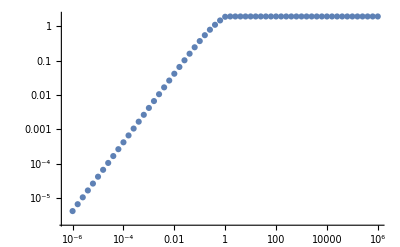

```mathematica
ListLogLogPlot[With[{x:=10^xp}, Table[{x,SupFac[d1, x]/pFavg}, {xp, -6,6, 0.2}]]]
```

## Capture Rates

### Geometric Limit

```mathematica
GeomLim[mχ_]:=Pi*(Rstar*km/hbarc)^2(1-B[1-ϵreg])/B[1-ϵreg]ρχ/mχ*Erf[Sqrt[3/2]vn/vd]/(vn*km);
GeomFD[dσ_,mx_?NumericQ]:= GeomLim[mx]*SupFac[dσ, mx];
```

```mathematica
ListLogLogPlot[{With[{x:=10^xp}, Table[{x,ΛAHFD[d1, 1570 , x]^4}, {xp, -4.8,5, 0.2}]], With[{x:=10^xp}, Table[{x,ΛAHFD[d10, 1570 , x]^4}, {xp, -4.8,5, 0.2}]]}]
```

-Graphics-

### Full Rates

```mathematica
Do[
Evaluate[Symbol[cap<>"CAP"]] =Interpolation[Import[StringJoin[{"../cap_rate/Mathematica_cap/", cap, "_cap.dat"}]]]
,
{cap, {"d0", "d1", "d2","d3","d4","d5","d6","d7", "d8", "d9", "d10"}}
]
```

## Heating Functions

```mathematica
fracCAP[dCAP_, mx_]:=(ToExpression[ToString[dCAP]<>"CAP"][Log10[mx]])/GeomLim[mx];
fracFD[dσ_, mx_]:=(ToExpression[ToString[dσ]<>"CAP"][Log10[mx]])/GeomFD[dσ,mx];
```

### Kinetic Heating

```mathematica
ΛKH[dCAP_,T_, mx_]:= 1570/T*(fracCAP[dCAP, mx])^(1/4);
ΛKHFD[dCAP_,T_, mx_]:= 1570/T*(fracFD[dCAP, mx])^(1/4);
```

### Annihilation Heating

```mathematica
ΛAH[dCAP_,T_, mx_]:= 2310/T*(fracCAP[dCAP, mx])^(1/4);
ΛAHFD[dCAP_,T_, mx_]:= 2310/T*(fracFD[dCAP, mx])^(1/4);
```

## Annihilation Rates

```mathematica
ΛAnn[ACS_,CAP_ ,mx_?NumericQ, temp_?NumericQ] :=((TT)^2*CAP[Log10[mx]]*ndAnFac[mx, temp]*ACS[mx, temp])^0.25;
```

```mathematica
Do[
Clear[out];

out = With[
{x:=10^xp},
Table[
Flatten[
{x,Table[
ΛAnn[ToExpression[oper<>"ACS"],ToExpression[oper<>"CAP"],  x,T],
 {T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}
]}
],
{xp, -4.8, 5, 0.05}
]
];
Export[StringJoin[ToString[oper], "ACS.dat"], out, "Table"]

,
{oper, {(*"d1","d2", "d3",*) "d4",(*, "d5", "d6", "d7",*) "d8"(*, "d9", "d10"*)}}
]
```

```mathematica
2^0.2
```

1.1487

## Plots

```mathematica
(*ssPlot = ListLogLogPlot[
 Evaluate@Table[
With[{x:=10^xp},
Table[{x,anG[d1ACS,d1CAP, x, T]*c12^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}
],

Joined->True, PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red},
AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"}, 
PlotLabel->"S-S", 
LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(*ppPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[d4ACS, x, T]*c34^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"PS-PS", LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(*vvPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[d5ACS, x, T]*c56^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"V-V", LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(*aaPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[d8ACS, x, T]*c78^2},{xp, -6, 6, 0.05}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"A-A", LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(*ttPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[d9ACS, x, T]*c910^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"T-T", LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(*groupedPlots =Legended[GraphicsGrid[{{ssPlot, ppPlot}, {vvPlot, aaPlot}, {ttPlot}}, ImageSize->Full ], LineLegend[Reverse[{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}],Reverse[{"10^1K","10^2K","10^3K","10^4K", "10^5K", "10^6K"}]]]*)
```

```mathematica
(*Export["ann-limits-fdsup.pdf", %]*)
```

## Neutrinos Stuff

```mathematica
ndAv = NIntegrate[nprof[x]*(1*^15)^3, {x, 0, 1}];
Gf = 1.166*1*^-5;
```

```mathematica
l[mx_, T_] :=1/(ndAv*Gf^2*(mx + mx/8*vAvg[mx, T])*hbarc^2)*1*^-3;
```

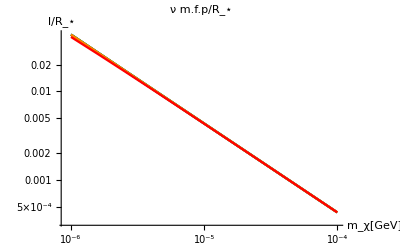

```mathematica
ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,l[x, T]/(rMax)},{xp, -6, -4, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "l/R_⋆"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"ν m.f.p/R_⋆", LabelStyle->Directive[Black,Bold]]
```

```mathematica
ndAv*10^-45
```

0.374505

```mathematica
l[10^-7, 10^3]/Rstar
```

0.434544

## Equilibrium time

```mathematica
(*τCA[Λ_,op_,TH_, TS_, mx_]:=(Λ[op, TH, mx]^4*6.58*^-25*3/(3.154*^7))/(ToExpression[ToString[op]<>"CAP"][Log10[mx]]*ndAnFac[mx, TS]*ToExpression[ToString[op]<>"ACS"][mx, TS])^0.5;*)
```

```mathematica
(*τCA[ΛKHFD, d1, 100, 1*^3, 10 ]*)
```

```mathematica
(*Do[
Clear[out];

out = With[
{x:=10^xp},
Table[
Flatten[
{x,Table[
τCA[ΛKHFD, ToExpression[oper], T, 1*^3, x ],
 {T, {100, 500, 1570}}
]}
],
{xp, -4.8, 5, 0.05}
]
];
Export[StringJoin[oper, "CA_eq_time_KHFD.dat"], out, "Table"]

,
{oper, {"d1","d2", "d3", "d4", "d5", "d6", "d7", "d8", "d9", "d10"}}
]
*)
```

```mathematica
(*Do[
Clear[out];

out = With[
{x:=10^xp},
Table[
Flatten[
{x,Table[
τCA[ΛAHFD, ToExpression[oper], T, 1*^3, x ],
 {T, {100, 500, 1570}}
]}
],
{xp, -4.8, 5, 0.05}
]
];
Export[StringJoin[oper, "CA_eq_time_AHFD.dat"], out, "Table"]

,
{oper, {"d1","d2", "d3", "d4", "d5", "d6", "d7", "d8", "d9", "d10"}}
]*)
```

```mathematica
(**)
```

```mathematica
(*densityList*)
```

## FD sup comparison

```mathematica
D8out = With[
{x:=10^xp},
Table[
Flatten[
{x,Table[
d8ACS[x, T],
 {T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}
]}
],
{xp, -4.8, 5, 0.05}
]
];
Export["d8_nosup.dat", D8out, "Table"];
Clear[D8out];
```

```mathematica
lepMasses[[2]]
quarkMasses
```

0.105658

{0.0022,0.0047,19/200,1.257,4.18,173}

```mathematica
?d8ACS
```

Global`d8ACS

d8ACS[mx_,temp_]:=∑_mf^Select[lepMasses,#1≤mx&] (1. mx^2 √(1.-mf^2/mx^2) fdSelect[mf][mx] (mf^2/mx^2+(1. (2.-mf^2/mx^2) vAvg[mx,temp])/12.))/(4. π c78^2)+∑_mf^Select[quarkMasses,#1≤mx&] (3. mx^2 √(1.-mf^2/mx^2) (mf^2/mx^2+(1. (2.-mf^2/mx^2) vAvg[mx,temp])/12.))/(4. π c78^2)

```mathematica
ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,1/d8ACS[x,T],{xp, -5, 6, 0.05}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"A-A", LabelStyle->Directive[Black,Bold]]
```